Autor: Adam Paździerz

# Metody numeryczne

## (kierunek Informatyka)

## Projekt 2

Metoda Newtona

Napisać procedurę realizującą algorytm metody stycznych (Newtona) (argumenty:  f, x_0,  e).
Napisać także procedurę realizującą algorytm metody Newtona dla układu dwóch równań nieliniowych (argumenty:  f, g, v_0,  e).

Korzystając z napisanych procedur:

a) Wyznaczyć pierwiastek 6 stopnia ze 101 z dokładnością 10^-10.

b) W pewnym układzie elektrycznym z diodą tunelową natężenie prądu i oraz napięcie u spełniają układ równań:

i=k u (u^2/3-3/2 u+2),
u/r+i=j,

gdzie k=1 mA/V^3, j=1 mA, r= 10 kΩ. Wykorzystując metodę Newtona wyznaczyć natężenie prądu oraz napięcie. Rozwiązanie zilustrować graficznie (można do tego celu wykorzystać instrukcję ContourPlot).

## Rozwiązanie

### Program (jedno równanie)

```mathematica
Clear[newton1];
newton1[f_,x0_,e_] :=Module[{xs = x0+2*e,xn=x0},
fp=D[f[x],{x}];
While[Abs[xn-xs]>e,
xs=xn;
xn=xs-f[xs]/fp/.{x->xs};
];
Return[xn//N];
]
```

### Przykład testowy (jedno równanie)

```mathematica
Clear[test1];
test1[x_]:= x^2 -3;
newton1[test1,2,10^-4]
```

1.73205

### Program (układ dwóch równań)

```mathematica
Clear[newton2];
newton2[f_,g_,v0_,e_] :=Module[{xs,xn,j,vo=v0,c,c1,h},

j={{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}};
vo=Transpose[{v0}];
xs=vo+2*e;
xn =vo;
While[Norm[xn-xs] >e,
xs=xn;
c=j/.{x->xs[[1,1]],y->xs[[2,1]]};
c1=Inverse[c];
h={f[x,y],g[x,y]} /.{x->xs[[1,1]], y->xs[[2,1]]};
xn=xs-c1.h;
];
Return[xn//N]
]
```

### Przykład testowy (układ dwóch równań)

```mathematica
Clear[f1];
Clear[f2];
f1[x_,y_]:= x^2+y^2;
f2 [x_,y_]:= x+2*x*y;
vo ={1,1};
newton2[f1,f2,vo,10^-4]
```

{{0.},{0.0000610352}}

### Zadanie a)

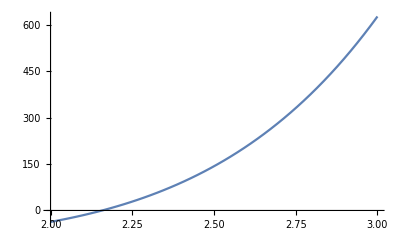

```mathematica
Clear[zadA];
zadA[x_] :=x^6-101;
Plot [zadA[x], {x,2,3}]
```

```mathematica
(*funkcja ma punkt zerujący funkcje w przedziale (2,3)*)
(*Obliczamy drugą pochodną i sprawdzamy jej znak *)
```

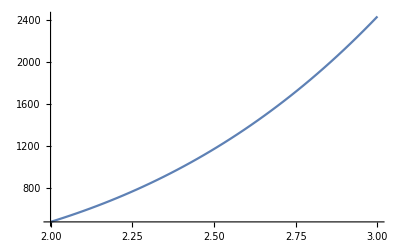

```mathematica
c =D[D[zadA[x],x],x];
Plot [c, {x,2,3}]
```

```mathematica
(* Zauważamy, że dla zadanego przedziału druga pochodna jest dodatnia *)
(* Więc wybieramy jako x0 =3,  bo w tym punkcie funkcja >0*)
```

```mathematica
newton1[zadA,3,10^-10]
```

2.15801

### Zadanie b)

```mathematica
Clear[A,B,j,k,r];
j=1;
k=1;
r=10;
A[u_,i_]:=k*u*(u^2/3 - 3*u/2 +2) -i;
B[u_,i_]:= j-u/r-i;
v={0.0,0.0};
newton2[A,B,v,10^-6]
```

{{2.38767},{0.761233}}

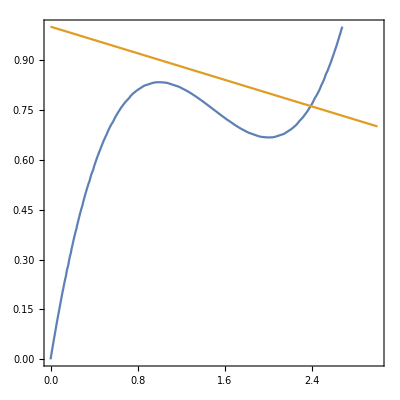

```mathematica
ContourPlot[{A[u,i] ==0, B[u,i]==0}, {u,0,3},{i,0,1}]
```